# Przykładowe grafu

## Ścieżki

```mathematica
pathDirOut="./figs/"
```

./figs/

```mathematica
If[!DirectoryQ[pathDirOut],CreateDirectory[pathDirOut]]
```

## Przykład grafu zupełnego

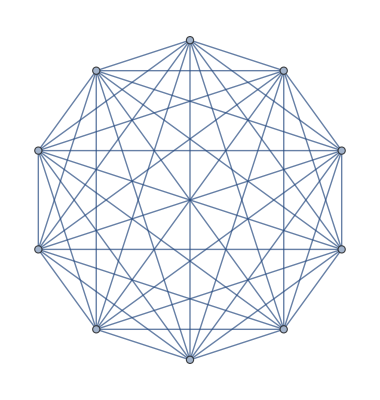

```mathematica
fig1=CompleteGraph[10]
```

```mathematica
Export[pathDirOut<>"graph_complete.pdf",fig1]
```

./figs/graph_complete.pdf

## Przykład grafu zupełnego k=1

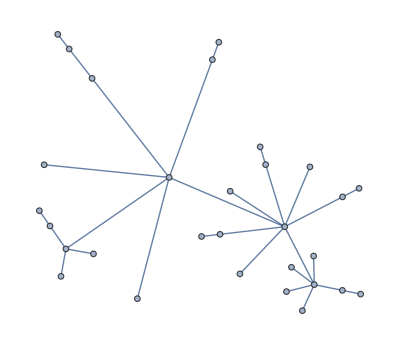

```mathematica
fig2=RandomGraph[BarabasiAlbertGraphDistribution[30,1],GraphLayout->"BalloonEmbedding"]
```

```mathematica
Export[pathDirOut<>"graph_ba.pdf",fig2]
```

./figs/graph_ba.pdf

## Przykład grafu zupełnego k=4

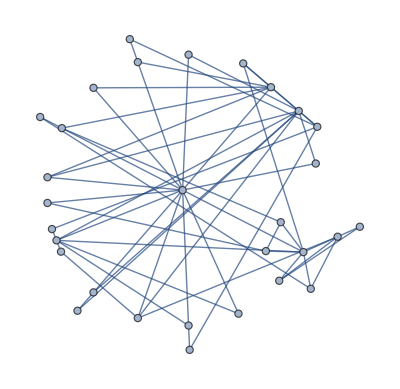

```mathematica
fig3=RandomGraph[BarabasiAlbertGraphDistribution[30,2],GraphLayout->"BalloonEmbedding"]
```

```mathematica
Export[pathDirOut<>"graph_ba_a.pdf",fig3]
```

./figs/graph_ba_a.pdf

## Init

```mathematica
SetDirectory[NotebookDirectory[]];
```